CONVERGENCIA EN LEY: APROXIMACIÓN DE DISTRIBUCIONES
TEOREMA CENTRAL DEL LÍMITE

La aproximación de distribuciones que estudiamos en este documento se basa en el concepto de  la convergencia en ley de una sucesión de variables aleatorias 

Definición: Sea {X_n} una sucesión de variables aleatorias definidas todas ellas sobre un mismo espacio de probabilidad. Diremos que la sucesión converge en ley o distribución hacia la variable aleatoria X, definida en el mismo espacio de probabilidad, si y solo si la correspondiente sucesión de funciones de distribución {F_n} converge hacia la función de distribución F de la variable aleatoria X en todo punto de continuidad de F.
lim_(n→∞)  F_X_n(x) = F_X(x)    ∀ x ∈ C(F_X)

Ejemplo: Sea X\[Distributed]Exp(a=2) y sea la sucesión {Y_n: n≥1} tal que 
Y_n=Piecewise[{{0, 0≤X<1-1/n}, {1
n, 1-1/n≤X<n
X≥n}}]
Estudiamos la convergencia en ley de esta sucesión.

Es claro que las variables aleatorias Y_n son discretas. Obtenemos la función de masa de estas variables

```mathematica
P[Yn=0]=P[0≤X<1-1/n]=∫_0^(1-1/n) 2*Exp[-2*x]ⅆx
```

1-ⅇ^(-2+2/n)

```mathematica
P[Yn=1]=P[1-1/n≤X<n]=∫_(1-1/n)^n 2*Exp[-2*x]ⅆx
```

ⅇ^(-2+2/n)-ⅇ^(-2 n)

```mathematica
P[Yn=n]=P[X≥n]=Integrate[2*Exp[-2*x], {x,n,+∞}]
```

ⅇ^(-2 n)

Obtenemos la función de distribución de cada variable Yn

```mathematica
G[x_,n_]:=Piecewise[{{0,x<0},{1-Exp[-2*(1-1/n)], 0≤x<1},{1-Exp[-2*n],1≤x<n},{1,x≥n}}]
```

```mathematica
G[x,n]
```

Piecewise[{{0, x<0}, {1-ⅇ^(-2 (1-1/n)), 0≤x<1}, {1-ⅇ^(-2 n), 1≤x<n}, {1, x≥n}, {0, True}}]

```mathematica
Manipulate[Plot[G[x,n],{x,-5,20}, PlotRange->{{-7,7},{0,1.1}},PlotStyle->{Purple, Thick},AxesLabel->{"x","G(x,n)"}],{n,1,25,1}]
```

Para cada x, calculamos el límite cuando n->+∞  de G[x,n]

```mathematica
G[x_]:=Limit[G[x,n], n->+∞]
```

```mathematica
G[x]
```

Piecewise[{{1, x≥1}, {1-1/ⅇ^2, 0≤x<1}, {0, True}}]

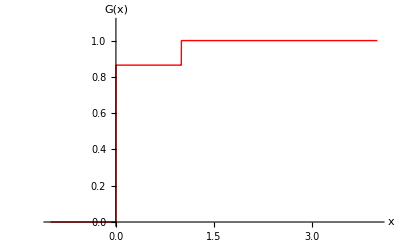

```mathematica
Plot[G[x],{x,-1,4}, PlotRange->{{-1,4},{0,1.1}},PlotStyle->{Red, Thick},AxesLabel->{"x","G(x)"}]
```

La función G(x) es una función de distribución correspondiente a una variable discreta, Y, que toma los valores 0 y 1 con probabilidades respectivas

```mathematica
P[Y=0]=G[0]-Limit[G[x],x->0, Direction->1]
```

1-1/ⅇ^2

```mathematica
P[Y=1]=G[1]-Limit[G[x],x->1, Direction->1]
```

1/ⅇ^2

La sucesión {Y_n: n≥1} converge en ley a la variable Y\[Distributed]Ber(p=1/ⅇ^2)

Teoremas de caracterización de la convergencia en ley para variables aleatorias discretas

Teorema 1: Si la sucesión de variables aleatorias {X_n} toma valores enteros no negativos, para todo n, entonces la condición necesaria y suficiente para que dicha sucesión converja en ley hacia una variable aleatoria discreta X es 
                                        lim_(n→∞) P(X_n=k) = P(X=k),          ∀ k∈ℕ
                                        
Teorema 2:   Si existe la función generatriz de probabilidad G_n(s) para cada una de  las variables aleatorias X_n, y existe la función generatriz de probabilidad de la variable aleatoria X, G_X(s), de la variable aleatoria límite, entonces
                                       lim_(n→∞) G_n(s) = G_X(s),                     
para todo s donde G_X(s) exista
                                       
 En este caso la sucesión {X_n} converge en ley o distribución hacia la variable aleatoria X

Aproximación de una distribución Binomial por una distribución de Poisson

La distribución de Poisson surgió como límite de la distribución Binomial de parámetros n y p,  Bi(n,p), con las siguientes condiciones: 
n->∞,  p->0 y además np->λ, con λ constante. 
En tales condiciones la distribución Binomial se puede aproximar por una distribución de Poisson de parámetro λ=np, Po(λ). (Teorema de Poisson, 1832)

Obsérvese que la media de la distribución Bi(n,p) es np que coincide con la media de la distribución Po(λ=np); sin embargo la varianza de la distribución Bi(n,p) es npq y la de la distribución de Po(λ=np) es np. Por lo tanto esta aproximación será más exacta cuanto más próximo a 1 sea q y por lo tanto cuanto más próximo a cero sea p.

Para su demostración hacemos uso del Teorema 1

```mathematica
Limit[PDF[BinomialDistribution[n,(λ/n)],x], n->∞]
```

Piecewise[{{(ⅇ^-λ λ^x)/Gamma[1+x], x≥0}, {0, True}}]

Mediante el teorema 2, debemos primero calcular la función generatriz de probabilidad de la distribución Binomial de parámetros n y donde p=λ/n

```mathematica
Expectation[s^x, x\[Distributed]BinomialDistribution[n,λ/n]]
```

(1+((-1+s) λ)/n)^n

Ahora calculamos el límite

```mathematica
Limit[%, n->∞]
```

ⅇ^((-1+s) λ)

Ejemplo: Supóngase que en una gran población la proporción de personas que tiene cierta enfermedad es del 1%. Determinar la probabilidad de que en un grupo aleatorio de 200 personas al menos 4 tengan la enfermedad.

Si llamamos X a la variable aleatoria X=”Número de personas que tiene la enfermedad en un grupo de 200 personas”, podemos decir que 
X∼Bi(n=200, p=0.01). Esta distribución cumple las condiciones dadas para poder aproximar la probabilidad que nos piden por una distribución de Poisson, Po(λ=200*0.01=2). La probabilidad pedida es 

P(X ≥ 4) = 1 - P(X < 4) = 1 - P(X ≤ 3)

```mathematica
1-CDF[BinomialDistribution[200, 0.01],3]
```

0.141966

```mathematica
N[1-CDF[PoissonDistribution[2],3]]
```

0.142877

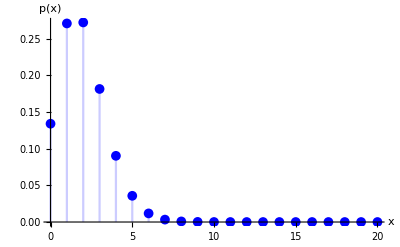

```mathematica
DiscretePlot[PDF[BinomialDistribution[200,0.01],k],{k,0,20},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}]
```

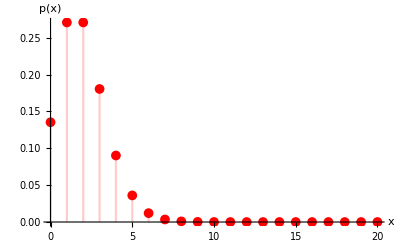

```mathematica
DiscretePlot[PDF[PoissonDistribution[2],k],{k,0,20},PlotStyle->Red,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}]
```

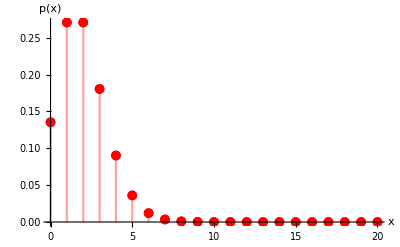

```mathematica
Show[%, %]
```

¿Qué ocurre cuando no se verifican las condiciones del teorema de Poisson?
Ejemplo: Supóngase que se realiza una sucesión de lanzamientos independientes de una moneda para la que la probabilidad de obtener cara es 0.70. Calcular la probabilidad de que en 20 lanzamientos se obtengan como máximo 10 caras.
Definimos la variable X=”número de caras en 20 lanzamientos de la moneda”, X∼Bi(n=20, p=0.7)
La probabilidad pedida es 

P(X ⩽ 20)

```mathematica
CDF[BinomialDistribution[20, 0.7], 10]
```

0.0479619

```mathematica
N[CDF[PoissonDistribution[14],10]]
```

0.175681

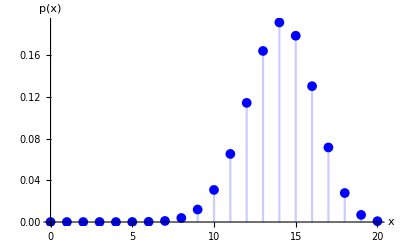

```mathematica
gb=DiscretePlot[PDF[BinomialDistribution[20,0.7],k],{k,0,20},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}]
```

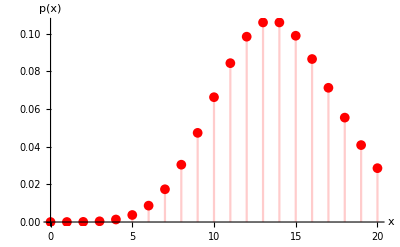

```mathematica
gp=DiscretePlot[PDF[PoissonDistribution[14],k],{k,0,20},PlotStyle->Red,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}]
```

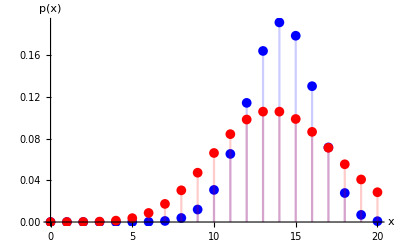

```mathematica
Show[gb,gp]
```

Teoremas de caracterización de la convergencia en ley para variables aleatorias absolutamente continuas

Teorema 1: Sean {X_n} y X variables aleatorias absolutamente continuas con funciones de densidad f_n y f respectivamente, tales que
 lim_(n→∞)  f_n(x) = f(x) para casi todo x. 
 Entonces la sucesión de variables aleatorias converge en ley hacia la variable aleatoria X.

Teorema 2: Sean {X_n} y X variables aleatorias absolutamente continuas con funciones de densidad f_n y f respectivamente, y funciones generatrices de momentos   M_n(t) y M(t), respectivamente, tal que  se verifica  lim_(n→∞)  M_n(t) = M(x) para todos los valores de t en un intervalo alrededor del punto 0. 
Entonces la sucesión de variables aleatorias converge en ley hacia la variable aleatoria X.

Este último teorema es válido tanto para variables aleatorias discretas como para variables aleatorias continuas.

No solo es posible aproximar distribuciones discretas por distribuciones discretas, también es posible hacer la aproximación de una distribución discreta por una distribución continua. En la mayoría de los casos por una distribución Normal.

Teorema Central del Límite

Este teorema es considerado en general como un nombre genérico aplicado a cualquier resultado que establezca la convergencia en distribución o en ley a la ley Normal para una suma creciente de variables aleatorias.

Definición: Sea {X_n} una sucesión de variables aleatorias independientes, definidas todas ellas sobre el mismo espacio de probabilidad, con medias y varianzas finitas. Diremos que la sucesión {X_n} obedece al teorema central del límite, si y solo si la sucesión {Z_n} converge en ley a una distribución N(0,1), siendo

```mathematica
Subscript[Z, n]=(Subscript[S, n]-E[Subscript[S, n]])/(σ(Subscript[S, n]))
```

con S_n=∑_(i=1)^n X_i

Teorema de De Moivre: Sea {X_n} una sucesión de variables aleatorias independientes e idénticamente distribuidas, cada una de ellas Bi(n=1,p) (Ber(p)). Entonces la sucesión obedece al teorema central del límite.

Para demostrar este teorema tenemos en cuenta que S_n∼Bi(n,p), por lo que  E(S_n)=np y V(S_n)=npq. Calculamos la función generatriz de momentos de las variables Z_n

```mathematica
MZ[n_]:=((1-p)*Exp[-(p*t/Sqrt[n*p*(1-p)])]+p*Exp[((1-p)*t/Sqrt[n*p*(1-p)])])^n
```

```mathematica
Limit[MZ[n], n->∞]
```

ⅇ^(t^2/2)

Que es la función generatriz de momentos de una distribución N(0,1).
Con esto estamos afirmando que cuando n es grande en una distribución Bi(n,p), la función de distribución  de la variable aleatoria tipificada se puede aproximar mediante la función de distribución de una N(0,1).

En realidad  lo que demuestra este teorema es que si X∼Bi(n,p) y n es grande, la distribución de X se puede aproximar mediante una distribución normal, N(np, √npq)

Ejemplo: Se lanza 100 veces una moneda equilibrada. Calcular la probabilidad de que el número de caras sea mayor que 50 y menor o igual que 60
 
Definimos la variable X=”número de caras en 100 lanzamientos de la moneda”, X∼Bi(n=100, p=0.5)
La probabilidad pedida es P(50<X ≤ 60)

Podemos dar dos soluciones:
- Una primera calculando de forma directa esta probabilidad mediante la función de distribución
- Aproximando la distribución de X por una N(100*0.5, √(100*0.5*0.5))

```mathematica
CDF[BinomialDistribution[100, 0.5], 60]-CDF[BinomialDistribution[100,0.5],50]
```

0.442605

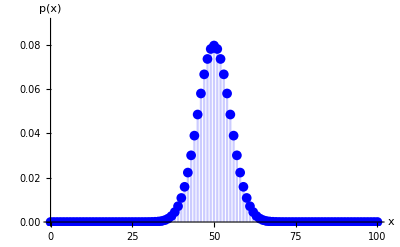

```mathematica
ab=DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,0,100},PlotStyle->Blue,PlotMarkers->{Automatic,Medium}, AxesLabel->{"x","p(x)"}, PlotRange->{{0,100},{0,0.09}}]
```

Utilizaremos la corrección por continuidad

```mathematica
N[CDF[NormalDistribution[50, 5], 60.5]-CDF[NormalDistribution[50,5],50.5]]
```

0.442308

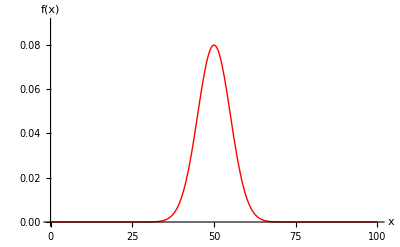

```mathematica
an=Plot[PDF[NormalDistribution[50,5],x],{x,0,100},PlotRange->{{0,100},{0,0.09}},PlotStyle->{Red, Thick},AxesLabel->{"x","f(x)"}]
```

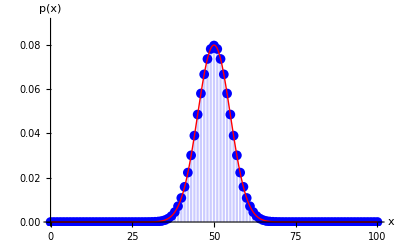

```mathematica
Show[ab,an]
```